## The QNMs of Schwarzschild black holes

```mathematica
(*This notebook compute the quasinormal modes of Schwarzschild black holes: the QN frequencies, the angular and radial functions. It is based on Refs.[1]-[3]. We use Leaver's units: M=1/2 here.*)
```

## Direct Integration

```mathematica
M=1;
l=2;
s=-2;
f[r_]:=1-2*M/r;
V=f[r]*(l*(l+1)/r^2+(1-s^2)*2*M/r^3);

EQ=f[r]^2 ψ''[r]+f'[r]f[r]ψ'[r]+(ω^2-V)ψ[r];
rsint=Integrate[1/f[r],r];imaginary=Im[rsint]/.r->20*M;rs=rsint-imaginary*I;rs/.r->10*M//N
```

14.1589

#### Series at the horizon

```mathematica
ORDH=20;
(*ψ[r_]:=(r-2*M)^(-I*2*M*ω)h[r];
f[r_]:=1-2*M/r;
EQ=f[r]^2 ψ''[r]+f'[r]f[r]ψ'[r]+(ω^2-V)ψ[r];
Simplify[EQ]*)
h[r_]:=Sum[hh[i] (r-2*M)^i,{i,0,ORDH+5}];
EQH=((-4 ⅈ M^2 ω+2 M r ω (ⅈ-2 M ω)+r^3 (-V+ω^2)) h[r]+(2 M-r) (M (-2+4 ⅈ r ω) h'[r]+(2 M-r) r h''[r]))/r^3;
ss=Simplify[Series[EQH,{r,2*M,ORDH}]];
eqsH=Table[SeriesCoefficient[ss,i]==0,{i,0,ORDH}];
yh=Table[hh[i],{i,1,ORDH+1}];
seriesH=Simplify[Solve[eqsH,yh]][[1]];
Length[yh]
Length[eqsH]
Clear[ψ,h]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

21

21

#### Series (infinity)

```mathematica
ORDINF=20;
(*ψ[r_]:=Exp[I ω r]g[r];

EQ=f[r]^2 ψ''[r]+f'[r]f[r]ψ'[r]+(ω^2-V)ψ[r];
Simplify[EQ]*)
g[r_]:=Sum[ginf[i]/r^i,{i,0,ORDINF+5}];
EQINF=g''[r] f[r]^2+g'[r] f'[r]f[r]+2 I ω f[r] g'[r]-V g[r];
ss=Simplify[Series[EQINF,{r,∞,ORDINF}]];
eqsINF=Table[SeriesCoefficient[ss,i]==0,{i,2,ORDINF}];
yinf=Table[ginf[i],{i,1,ORDINF-1}];
seriesINF=Simplify[Solve[eqsINF,yinf]][[1]];
```

#### Integration

```mathematica
INT[ω0_,rm0_,EPS0_,INF0_]:=(
ruleP={AccuracyGoal->12,PrecisionGoal->12};
param={ω->ω0,hh[0]->1,ginf[0]->1};
EPS=EPS0;
rinf=INF0*2*M/.param;
rhn=(1+EPS)2*M;
(****INTEGRATION FROM THE HORIZON***)
ψgH=(r-2*M)^(-I*2*M*ω)Sum[hh[i] (r-2*M)^i,{i,0,ORDH-1}]//.Union[param,seriesH];
BCs={ψ[rhn]==ψgH/.r->rhn,ψ'[rhn]==D[ψgH,r]/.r->rhn};
EQs={(ω^2-V) ψ[r]+f'[r]f[r] ψ'[r]+f[r]^2 ψ''[r]==0}/.param;
rm=rm0;
solH=NDSolve[Union[EQs,BCs],ψ,{r,rhn,rm},ruleP];
ψnH=ψ[r]/.solH[[1]];
ψnHp=D[ψnH,r];
(*******)
(***INTEGRATION FROM INFINITY****)
(*tortoise coordinate*)
ψgINF=Exp[I ω rs]Sum[ginf[i]/r^i,{i,0,ORDINF-1}]//.Union[param,seriesINF];
BCs={ψ[rinf]==ψgINF/.r->rinf,ψ'[rinf]==D[ψgINF,r]/.r->rinf};
EQs={(ω^2-V) ψ[r]+f'[r]f[r] ψ'[r]+f[r]^2 ψ''[r]==0}/.param;
rm=rm0;
solINF=NDSolve[Union[EQs,BCs],ψ,{r,rinf,rm},ruleP];
ψnINF=ψ[r]/.solINF[[1]];
ψnINFp=D[ψnINF,r];
(*******)
b=ψnH/ψnINF/.r->rm;(*we fix the coefficients of the linear combination in order for ψn to be continuous at r=rm*)
ψn=Piecewise[{{ψnH,r<rm},{b ψnINF,r≥rm}}];
Δψp=(D[ψnH,r]-D[b ψnINF,r])/D[ψnH,r]/.r->rm;
{Δψp}(*the function INT returns the jump of the first derivative at the matching point for a given ω*)
);
```

```mathematica
INT[1,3,0.001,20]
```

{2.00007-0.00526877 ⅈ}

```mathematica
ωguess=0.37-0.08I;
f4[y_?NumericQ]:=INT[y,(*rm*)4,10^-4,(*rinf*)10][[1]];
y0n=y/.FindRoot[f4[y]==0,{y,ωguess}][[1]];
check=Abs[f4[y0n]];
{y0n,check}
```

{0.373673-0.088961 ⅈ,2.67204×10^-10}

## Continued Fractions

### Fundamental mode

```mathematica
(*We first set the parameters of the Kerr spacetime, the field and the mode we're interested in:*)
 s=-2;
m=0;
l=2;
M=1;
epsilon=s^2-1;
rho=-2*M*I*w;

winit=0.37-0.08ⅈ;(*This is an initialization for the frequency*)
```

```mathematica
NITMAX=350;
γ=Function[n,n^2+4*rho*n+4*rho^2-epsilon-1];
β=Function[n,-(2*n^2+(8*rho+2)*n+8*rho^2+4*rho+l*(l+1)-epsilon)];
α=Function[n,n^2+(2*rho+2)*n+2*rho+1];
Leaver31[w_]:=Module[{Rn},
For[{n=NITMAX;Rn=-1.0;},
n>0,
{
Rn=γ[n]/(β[n]-α[n]*Rn);n--;}
];Rn];Leaverfund[w_]:=β[0]/α[0]-Leaver31[w];wang0=FindRoot[Leaverfund[w]==0,{w,winit}][[1]][[2]]
```

0.373672-0.0889623 ⅈ

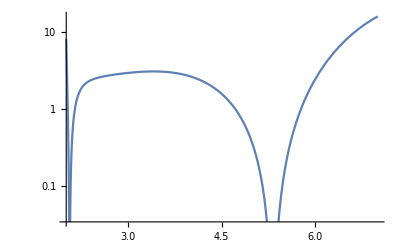

```mathematica
PAR=wang0;
ae[0]=1;
ae[1]=-β[0]/α[0]/.w->PAR;
i=1;While[i<NITMAX,ae[i+1]=(-β[i]*ae[i]-γ[i]*ae[i-1])/(α[i])/.w->PAR;i=i+1];

Psi=(r-2*M)^(rho)*r^(-2*rho)*Exp[-rho*(r-2*M)]*Sum[ae[i]*((r-2*M)/r)^(i),{i,0,NITMAX-1}]/.w->PAR;
LogPlot[Im[Psi]^2,{r,2.01,7}]
```

### First overtone

```mathematica
Leaver3o1[w_]:=Module[{Rn},For[{n=NITMAX;Rn=-1.0;},n>1,{Rn=γ[n]/(β[n]-α[n]*Rn);n--;}
];Rn];

Leaver1[w_]:=β[1]/α[1]-(α[0]γ[1])/(α[1]β[0])-Leaver3o1[w];wang1=FindRoot[Leaver1[w]==0,{w,0.34-0.27*I}][[1]][[2]]
```

0.346711-0.273915 ⅈ

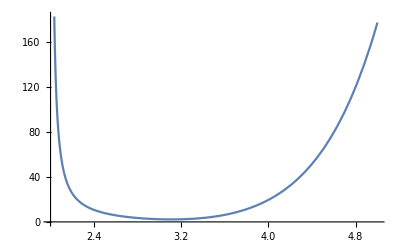

```mathematica
PAR1=wang1;
ae1[0]=1;
ae1[1]=-β[0]/α[0]/.w->PAR1;

i=1;While[i<NITMAX,ae1[i+1]=(-β[i]*ae1[i]-γ[i]*ae1[i-1])/(α[i])/.w->PAR1;i=i+1];
Psi1=(r-2*M)^(rho)*r^(-2*rho)*Exp[-rho*(r-2*M)]*Sum[ae1[i]*((r-2*M)/r)^(i),{i,0,NITMAX-1}]/.w->PAR1;
Plot[Abs[Psi1]^2,{r,2,5}]
```

### Second overtone:

```mathematica
Leaver3o2[w_]:=Module[{Rn},For[{n=NITMAX;Rn=-1.0;},n>2,{Rn=γ[n]/(β[n]-α[n]*Rn);n--;}
];Rn];
Leaver2[w_]:=β[2]/α[2]-(α[1]γ[2])/(α[2](β[1]-(α[0]γ[1])/β[0]))-Leaver3o2[w];wang2=FindRoot[Leaver2[w]==0,{w,0.3010534546123664-0.4782769832230718*I}][[1]][[2]]
```

0.301053-0.478277 ⅈ

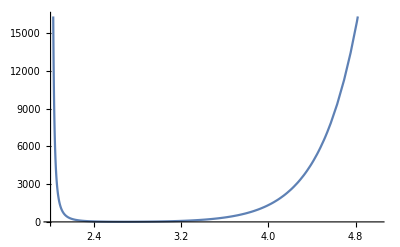

```mathematica
PAR2=wang2;
ae2[0]=1;
ae2[1]=-β[0]/α[0]/.w->PAR2;

i=1;While[i<NITMAX,ae2[i+1]=(-β[i]*ae2[i]-γ[i]*ae2[i-1])/(α[i])/.w->PAR2;i=i+1];
Psi2=(r-2*M)^(rho)*r^(-2*rho)*Exp[-rho*(r-2*M)]*Sum[ae2[i]*((r-2*M)/r)^(i),{i,0,NITMAX-1}]/.w->PAR2;
Plot[Abs[Psi2]^2,{r,2,5}]
```

### Inversion kth:

```mathematica
k=3;

Leaver3o1[w_]:=Module[{Rn},For[{n=NITMAX;Rn=-1.0;},n>k,{Rn=γ[n]/(β[n]-α[n]*Rn);n--;}
];Rn];

Leaver1[w_]:=β[1]/α[1]-(α[0]γ[1])/(α[1]β[0])-Leaver3o1[w];


Leaverk[w_]:=Module[{Rn},For[{n=0;Rn=0;},n<k+1,{Rn=(α[n-1]γ[n])/(β[n-1]-Rn);n++;}
];Rn];
wang1=FindRoot[β[k]/α[k]-1/α[k]*Leaverk[w]-Leaver3o1[w]==0,{w,0.07+0.2*I}][[1]][[2]]
```

0.207515-0.946845 ⅈ

## References

```mathematica
[1] S. Chandrasekhar and S. Detweiler "The quasi-normal modes of the Schwarzschild black hole". Proc. R. Soc. Lond.A344: 441(1975).
```

```mathematica
[2] E. Leaver, "An analytic representation for the quasi-normal modes of kerr black holes". Proc. R. Soc. Lond.A402: 285(1985).
```

```mathematica
[3]E. Berti, V. Cardoso and C. M. Will, "On gravitational-wave spectroscopy of massive black holes with the space interferometer LISA", Phys. Rev. D73:064030 (2006). [arXiv: gr-qc/0512160].
```

```mathematica
[4]E. Berti, V. Cardoso and M. Casals, "Eigenvalues and eigenfunctions of spin-weighted spheroidal harmonics in four and higher dimensions", Phys. Rev. D73:024013 (2006); Erratum-ibid.D73:109902 (2006). [arXiv: gr-qc/0511111].
```

```mathematica
[5]E. Berti, V. Cardoso and A. Starinets, "Quasinormal modes of black holes and black branes", Class.Quant.Grav.26 (2009) 163001
```

```mathematica
[6]https://centra.tecnico.ulisboa.pt/network/grit/files/
```